# Taylor and Laurent Series

TS(z)=∑_(k=0)^∞ (a_k(z-z_0))^k on disk 𝒟={z:|z-z_0|<R}
where f is analytic on 𝒟 and c is any simple CCW contour inside 𝒟 
	a_k=(f^(k)(z_0))/(k!)=1/(2π ⅈ)∫_c (f(ζ))/(ζ-z_0)^(k+1)dζ.

LS(z)=∑_(k=-∞)^∞ (a_k(z-z_0))^k on annulus 𝒜={z:R_1< |z-z_0|< R_2}
where f is analytic on 𝒜 and c is any simple CCW contour inside 𝒜 
	a_k=(f^(k)(z_0))/(k!)=1/(2π ⅈ)∫_c (f(ζ))/(ζ-z_0)^(k+1)dζ.

### Example 4.26 p111: f[z]=√(z^2-1)

#### f[z]=√(z^2-1)=z(1-1/z^2)^(1/2)

This version is analytic everywhere except the branch cut along the real axis from -1 to 1.  We can compute the Laurent Series around z=0 using the binomial series which converges for |x|<1
	(1+x)^α=∑_(k=0)^∞ (α
k)x^k=1+α x+(α(α-1))/(2!)x^2+(α(α-1)(α-2))/(3!)x^3+…
with α=1/2.  In detail
	(z(1-1/z^2))^(1/2)=z∑_(k=0)^∞ (1/2
k)(-1/z^2)^k
so the Laurent Series is
	(z(1-1/z^2))^(1/2)=z(1-1/2 z^-2-1/8 z^-4-1/16 z^-6-5/128 z^-8-…)
It should be good in a donut including both branch points.

```mathematica
Clear[LS,n,z]
LS[n_][z_]:=z*Sum[Binomial[1/2,k](-1/z^2)^k,{k,0,n}]
LS[5][z]
```

(1-7/(256 z^10)-5/(128 z^8)-1/(16 z^6)-1/(8 z^4)-1/(2 z^2)) z

```mathematica
f1[z_]:=z(1-1/z^2)^(1/2);
n=7;
TabView[{
"Paste"->Show[
ComplexPlot3D[LS[n][z],{z,2},
RegionFunction->Function[z,Abs[z-0]>1.1]],
ComplexPlot3D[f1[z],{z,2},
RegionFunction->Function[z,Abs[z-0]<1.05]]],
"Error"->ComplexPlot3D[(LS[n][z]-f1[z])/Abs[f1[z]],{z,2},
RegionFunction->Function[z,Abs[z-0]>1.1],PlotRange->All]
}]
```

12

#### f[z]=√(z^2-1)=ⅈ √(1-z^2)

This version is analytic everywhere except the branch cut along the real axis from –∞ to -1 and from 1 to ∞.  We should be able to compute the Taylor series about z=0. The radius of convergence should be 1. In detail
	(ⅈ(1-z^2))^(1/2)=ⅈ∑_(k=0)^∞ (1/2
k)(-z^2)^k
so the Taylor Series is
	(ⅈ(1-z^2))^(1/2)=ⅈ(1-1/2 z^2-1/8 z^4-1/16 z^6-5/128 z^8-…)
It should be good in a disk of radius 1.

```mathematica
TS[n_][z_]:=ⅈ*Sum[Binomial[1/2,k](-z^2)^k,{k,0,n}]
TS[5][z]
```

ⅈ (1-z^2/2-z^4/8-z^6/16-(5 z^8)/128-(7 z^10)/256)

```mathematica
n=6;
f2[z_]:=ⅈ (1-z^2)^(1/2)
TabView[{
"paste"->Show[
ComplexPlot3D[f2[z],{z,2},
RegionFunction->Function[z,Abs[z-0]>1.0]],
ComplexPlot3D[TS[n][z],{z,1},
RegionFunction->Function[z,Abs[z-0]<0.9]]
],
"error"->ComplexPlot3D[(TS[n][z]-f2[z])/Abs[f2[z]],{z,1},
RegionFunction->Function[z,Abs[z-0]<0.9],
PlotRange->All]}
]
```

12

Just a reminder the various versions have different branch cuts.

```mathematica
TabView[{
"f1"->ComplexPlot3D[f1[z],{z,2}],
"f2"->ComplexPlot3D[f2[z],{z,2}]
}]
```

12

### Example 4.24 p109: f[z]=1/((z-1)(z-2))

Looks a little weird three different expansions about z=0.   Note 
	1/((z-1)(z-2))=1/(z-2)-1/(z-1)  (reminder how on the board)

#### Taylor Series z=0

Since 
	1/(z-2)=-1/2 1/(1-z/2)=-1/2∑_(k=0)^∞ (z/2)^k  and -1/(z-1)=1/(1-z)=∑_(k=0)^∞ z^k 
the TS about z=0 is
	∑_(k=0)^∞ z^k-1/2(z/2)^k=1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32+…
which converges for |z|<1.

```mathematica
Clear[TS,n,z]
f[z_]:=1/((z-1)(z-2))
TS[n_][z_]:=Sum[z^k-1/2(z/2)^k,{k,0,n}]
n=5;
TS[n][z]
Series[f[z],{z,0,n}]
```

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32+(63 z^5)/64

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32+(63 z^5)/64+O[z]^6

```mathematica
n=8;
g[z_]=TS[n][z]
TabView[{
"paste"->Show[
ComplexPlot3D[f[z],{z,3},
RegionFunction->Function[z,Abs[z]>0.8]],
ComplexPlot3D[g[z],{z,1},
RegionFunction->Function[z,Abs[z]<0.8]]],
"error"->ComplexPlot3D[(g[z]-f[z])/Abs[f[z]],{z,1},
RegionFunction->Function[z,Abs[z]<0.8],
PlotRange->All]
}]
```

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32+(63 z^5)/64+(127 z^6)/128+(255 z^7)/256+(511 z^8)/512

12

#### Laurent Series z=0 1 < |z|< 2

For |z|<2 
	1/(z-2)=-1/2 1/(1-z/2)=-1/2∑_(k=0)^∞ (z/2)^k. 
For |z|>1 we have  
	1/(z-1)=1/z 1/(1/z-1)=1/z 1/(1-1/z)=1/z∑_(k=0)^∞ (1/z)^k 
the LS we want follows from
	1/((z-1)(z-2))=1/(z-2)-1/(z-1)=-1/2 1/(1-z/2)-1/z 1/(1-1/z)
	LS(z)=-∑_(k=0)^∞ (1/z)^(k+1)-1/2∑_(k=0)^∞ (z/2)^k
which converges (slowly)  for 1 < |z|< 2.

```mathematica
Clear[TS,n,z]
f[z_]:=1/((z-1)(z-2))
LS1[n_][z_]:=Sum[-1/2(z/2)^k-(1/z)^(k+1),{k,0,n}]
```

```mathematica
n=5;
g[z_]=LS1[n][z]
TabView[{
"paste"->Show[
ComplexPlot3D[f[z],{z,3},
RegionFunction->Function[z,Or[Abs[z]<1.1,Abs[z]>1.8]]],
ComplexPlot3D[g[z],{z,2},
RegionFunction->Function[z,1.1<Abs[z]<1.8]]],
"error"->ComplexPlot3D[(g[z]-f[z])/Abs[f[z]],{z,2},
RegionFunction->Function[z,1.1<Abs[z]<1.8],
PlotRange->All]
}]
```

-1/2-1/z^6-1/z^5-1/z^4-1/z^3-1/z^2-1/z-z/4-z^2/8-z^3/16-z^4/32-z^5/64

12

#### Laurent Series z=0 |z| > 2

We have
	1/(z-2)=1/z 1/(1-2/z)=1/z∑_(k=0)^∞ (2/z)^k. 
and
	1/(z-1)=1/z 1/(1/z-1)=1/z 1/(1-1/z)=1/z∑_(k=0)^∞ (1/z)^k 
so the LS is 
	1/((z-1)(z-2))=1/(z-2)-1/(z-1)=1/z 1/(1-2/z)-1/z 1/(1-1/z)
	LS(z)=-∑_(k=0)^∞ (1/z)^(k+1)+1/z∑_(k=0)^∞ (2/z)^k
which converges for |z|> 2.

```mathematica
Clear[TS,n,z]
f[z_]:=1/((z-1)(z-2))
LS2[n_][z_]:=Sum[1/z(2/z)^k-(1/z)^(k+1),{k,0,n}]
```

```mathematica
n=8;
g[z_]=LS2[n][z]
TabView[{
"paste"->Show[
ComplexPlot3D[f[z],{z,3},
RegionFunction->Function[z,Abs[z]<2.1]],
ComplexPlot3D[g[z],{z,3},
RegionFunction->Function[z,Abs[z]>2.2]]],
"error"->ComplexPlot3D[(g[z]-f[z])/Abs[f[z]],{z,3},
RegionFunction->Function[z,Abs[z]>2.2],
PlotRange->All]
}]
```

255/z^9+127/z^8+63/z^7+31/z^6+15/z^5+7/z^4+3/z^3+1/z^2

12

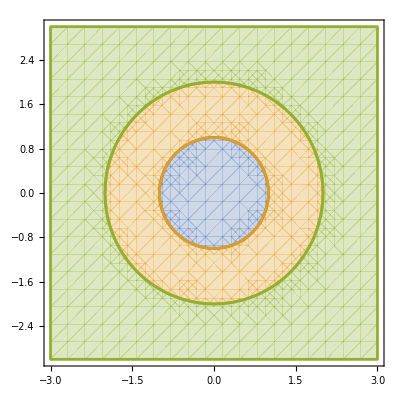

```mathematica
ComplexRegionPlot[ {
Abs[z]<1,
1<Abs[z]<2,
Abs[z]>2
},{z,3}]
```

### Example 4.25 p109: f[z]=ⅇ^(z-1/z)

f(z)=ⅇ^z.ⅇ^(-1/z)

```mathematica
Clear[f,g,z,n,LS]
f[z_]:=ⅇ^z ⅇ^(-1/z)
n=6;
g[z_]=Normal[Series[E^z,{z,0,n}]];
LS[z_]=Expand[g[z]*g[-1/z]]
{R1,R2,ϵ}={0.5,1.8,0.01};
TabView[{
"paste"->Show[
ComplexPlot3D[f[z],{z,2},
RegionFunction->Function[z,Or[R1-ϵ>Abs[z],Abs[z]>R2+ϵ]]],
ComplexPlot3D[f[z],{z,2},
RegionFunction->Function[z,R1<Abs[z]<R2]]],
"error"->ComplexPlot3D[(f[z]-LS[z])/Abs[f[z]],{z,2},
RegionFunction->Function[z,R1<Abs[z]<R2],
PlotRange->All]
}]
```

23213/103680+1/(720 z^6)-1/(144 z^5)+49/(1440 z^4)-557/(4320 z^3)+6097/(17280 z^2)-49829/(86400 z)+(49829 z)/86400+(6097 z^2)/17280+(557 z^3)/4320+(49 z^4)/1440+z^5/144+z^6/720

12